```mathematica
(*SetDirectory[];
SetDirectory["~/Downloads/mcmc/LevelScheme"];
Get["LevelScheme`"];
PlotOptions1={FrameTicks->{LinTicks,LinTicks,LinTicks,LinTicks},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{25,FontFamily->"Helvetica"}};
PlotOptions12Ticks={FrameTicks->{LinTicks,LinTicks,None,None},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{25,FontFamily->"Helvetica"}};
PlotOptions12TicksSmaller={FrameTicks->{LinTicks,LinTicks,None,None},FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[15],LabelStyle->{15,FontFamily->"Helvetica"}};*)
```

```mathematica
PlotOptions1={Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{25,FontFamily->"Helvetica"}}
```

{Frame→True,FrameStyle→Directive[Thickness[Large],Dashing[2]],FrameTicksStyle→Directive[30],LabelStyle→{25,FontFamily→Helvetica}}

```mathematica
fS=24;
pDisco[col_,testo_]={Graphics[{col,Thickness[0.1],Disk[{0.6,0.2},0.7]},ImageSize-> 40,PlotRange-> {{-2,2},{-2,2}}],Text[Style[testo,fS,FontFamily->Helvetica]]};
pRectangle[col_,testo_]={Graphics[{col,Thickness[0.1],Rectangle[{0,0}]},ImageSize-> 40,PlotRange-> {{-2,2},{-2,2}}],Text[Style[testo,fS,FontFamily->Helvetica]]};
linea[col_,ltype_,n_,t_,testo_]:={Graphics[{col,ltype,Opacity[n],Thickness[t],Line[{{0,-0.4},{1,-0.4}}]},ImageSize-> 40,AspectRatio-> 0.1],Text[Style[testo,fS,FontFamily->Helvetica]]};
```

```mathematica
(*Set your own working directory directory here; "DR7ShenZUMiLM3000.txt" needs to be in this folder *)
SetDirectory["/../../export/data1/caplarn/Documents/Eddington/DataandNB/Shen05/"]
```

/export/data1/caplarn/Documents/Eddington/DataandNB/Shen05

```mathematica
(*Total Shen07 catalog, all sources*)
data=Drop[Import["DR7ShenZUMiLM3000.txt","Table"],1][[All,{2,1,3,4,5,6}]] ;
(*Total Shen07 catalog, uniform sample*)
dataUniform=Select[data,First[#]==1&][[All,{2,3,4,5,6}]];
(*Total Shen07 catalog, uniform sample between redshift 0.3 and 5*)
dataraw=Select[dataUniform,0.3≤First[#]≤5&][[All,{1,2,3,4,5}]];
```

```mathematica
data05=Select[dataraw,0.4≤First[#]≤0.6&][[All,{2,3,4}]];
data10=Select[dataraw,0.9≤First[#]≤1.1&][[All,{2,3,4}]];
data18=Select[dataraw,1.7≤First[#]≤1.9&][[All,{2,3,4}]];
```

```mathematica
data05=Select[data05,#[[3]]>7&];
data10=Select[data10,#[[3]]>7&];
data18=Select[data18,#[[3]]>7&];
```

### Procedure to create plot with total luminosities

```mathematica
dataz={data05,data10,data18};
j=1;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta1=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=2;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta2=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=3;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta3=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
```

```mathematica
marker1=Graphics[{Blue,Disk[]}];marker2=Graphics[{Orange,Disk[]}];marker3=Graphics[{Red,Disk[]}];
```

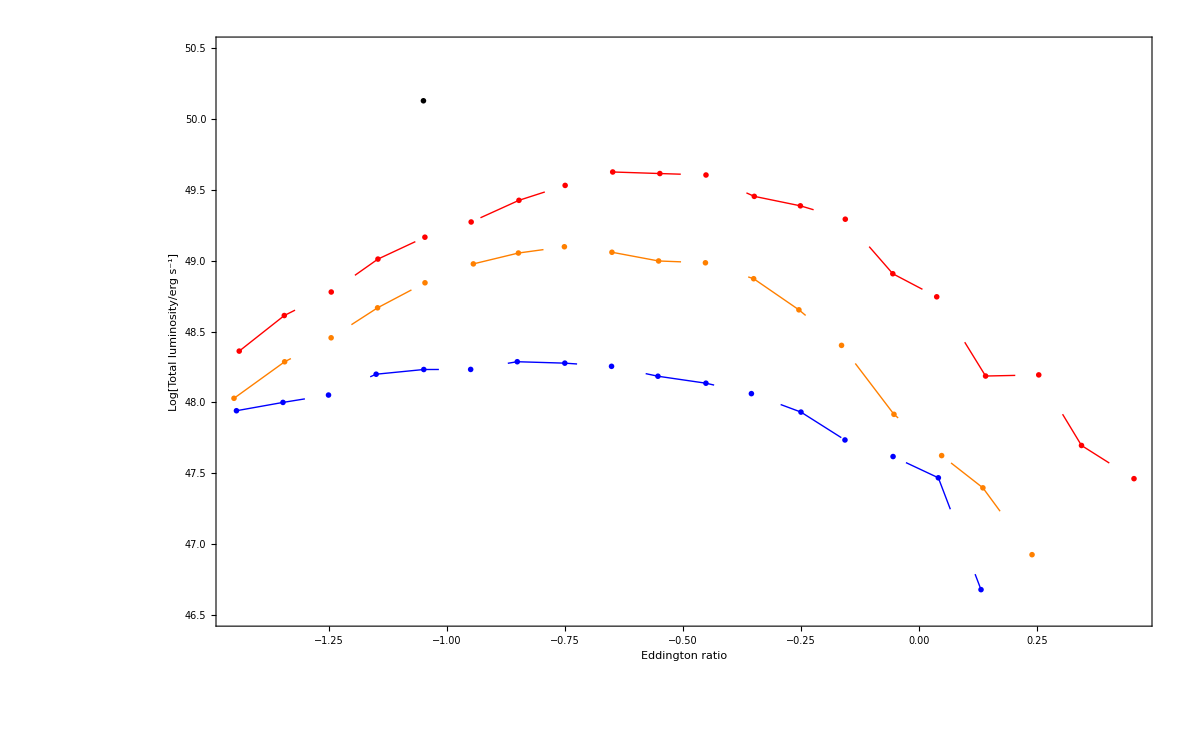

```mathematica
ListPlot[{LumWeightLamdta1,LumWeightLamdta2,LumWeightLamdta3},PlotRange->{46.5,50.5},PlotStyle->{{Blue,Thick,Dashing[2]},{Orange,Thick,Dashing[2]},{Red,Thick,Dashing[2]}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},Joined->True,FrameLabel->{"Eddington ratio","Log[Total luminosity/erg s^-1]"},PlotOptions1,PlotMarkers->{{marker1,0.015},{marker2,0.015},{marker3,0.015}}, Epilog->{Inset[Grid[{linea[Blue,{},5,0.1,Style["0.4<z<0.6",FontFamily->Helvetica]],linea[Orange,{},5,0.1,Style["0.9<z<1.1",FontFamily->Helvetica]],linea[Red,{},5,0.1,Style["1.7<z<1.9",FontFamily->Helvetica]]},Spacings->{0,0},Alignment-> Left],{-1.05,50.13}]},ImageSize->1200]
```

### Procedure to create plot with total luminosities and error bars

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
j=1;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta1=Select[Table[If[Length[SplitByEddRatio[[i]]]>0,{Mean[SplitByEddRatio[[i]][[All,3]]],ListOfTotalLum=Log10[Table[Total[RandomChoice[Power[10,SplitByEddRatio[[i]][[All,1]]],Length[SplitByEddRatio[[i]]]]],{j,100}]];Mean[ListOfTotalLum],StandardDeviation[ListOfTotalLum]},-99],{i,20}],Length[#]>1&];
LumWeightLamdta1ForPlot={{LumWeightLamdta1[[All,1]],LumWeightLamdta1[[All,2]]}//Transpose,ErrorBar[#]&/@LumWeightLamdta1[[All,3]]}//Transpose;
j=2;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta2=Select[Table[If[Length[SplitByEddRatio[[i]]]>0,{Mean[SplitByEddRatio[[i]][[All,3]]],ListOfTotalLum=Log10[Table[Total[RandomChoice[Power[10,SplitByEddRatio[[i]][[All,1]]],Length[SplitByEddRatio[[i]]]]],{j,100}]];Mean[ListOfTotalLum],StandardDeviation[ListOfTotalLum]},-99],{i,20}],Length[#]>1&];
LumWeightLamdta2ForPlot={{LumWeightLamdta2[[All,1]],LumWeightLamdta2[[All,2]]}//Transpose,ErrorBar[#]&/@LumWeightLamdta2[[All,3]]}//Transpose;
j=3;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta3=Select[Table[If[Length[SplitByEddRatio[[i]]]>0,{Mean[SplitByEddRatio[[i]][[All,3]]],ListOfTotalLum=Log10[Table[Total[RandomChoice[Power[10,SplitByEddRatio[[i]][[All,1]]],Length[SplitByEddRatio[[i]]]]],{j,100}]];Mean[ListOfTotalLum],StandardDeviation[ListOfTotalLum]},-99],{i,20}],Length[#]>1&];
LumWeightLamdta3ForPlot={{LumWeightLamdta3[[All,1]],LumWeightLamdta3[[All,2]]}//Transpose,ErrorBar[#]&/@LumWeightLamdta3[[All,3]]}//Transpose;
```

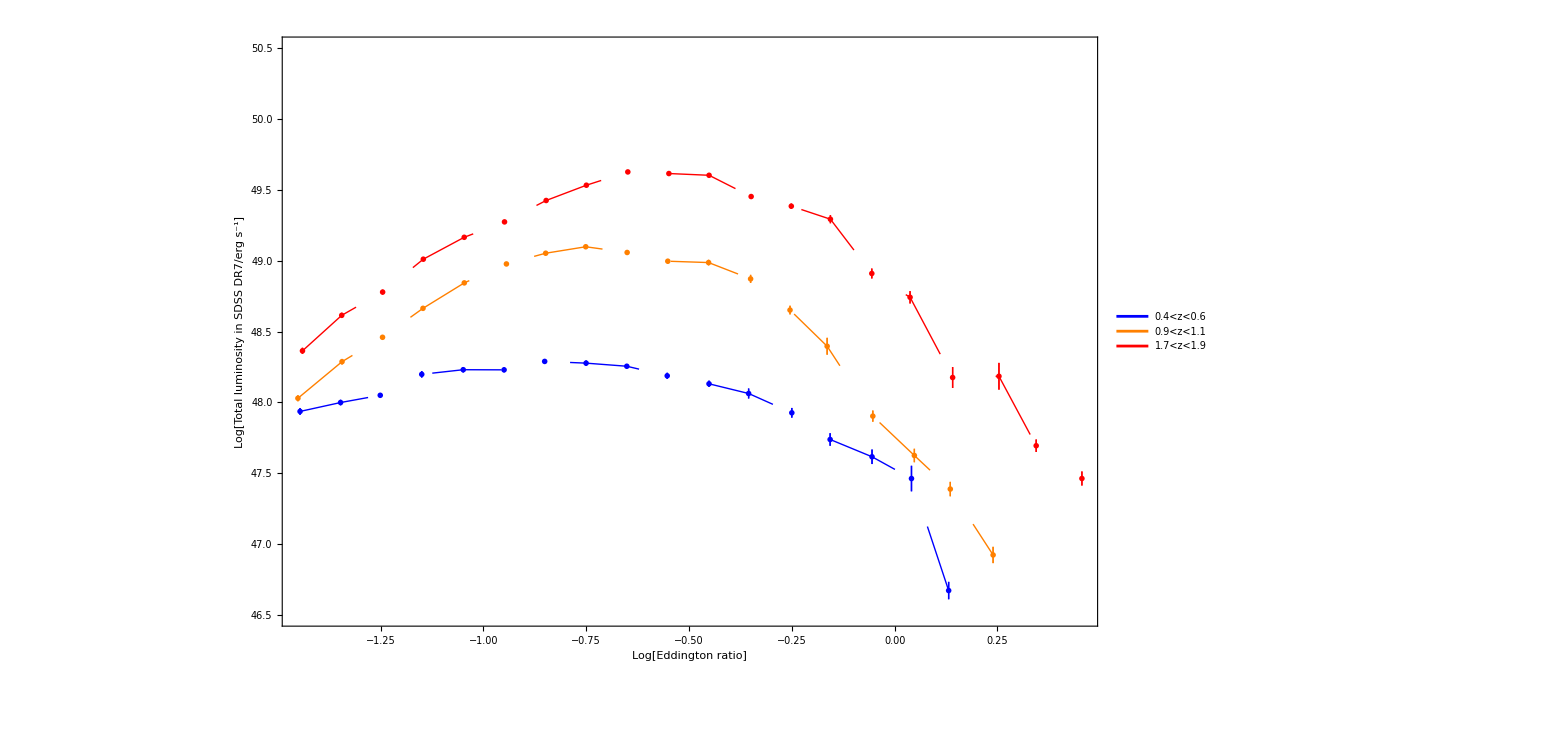

```mathematica
ErrorListPlot[{LumWeightLamdta1ForPlot,LumWeightLamdta2ForPlot,LumWeightLamdta3ForPlot},PlotRange->{46.5,50.5},PlotStyle->{{Blue,Thick,Dashing[2]},{Orange,Thick,Dashing[2]},{Red,Thick,Dashing[2]}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},Joined->True,FrameLabel->{"Log[Eddington ratio]","Log[Total luminosity in SDSS DR7/erg s^-1]"},PlotOptions1,PlotMarkers->{{marker1,0.015},{marker2,0.015},{marker3,0.015}}, Epilog->{Inset[Grid[{linea[Blue,{},5,0.1,Style["0.4<z<0.6",FontFamily->Helvetica]],linea[Orange,{},5,0.1,Style["0.9<z<1.1",FontFamily->Helvetica]],linea[Red,{},5,0.1,Style["1.7<z<1.9",FontFamily->Helvetica]]},Spacings->{0,0},Alignment-> Left],{-1.05,50.13}](*,Inset[Rotate[Style["Eddington limit",24,FontFamily->Helvetica],-π/2],{0.05,49.83}]*)},ImageSize->1200]
```

### Procedure to create plot with fractional luminosities and error bars

```mathematica
i=1;
ListOfTotalFractionalLum=Log10[Table[Total[RandomChoice[Power[10,SplitByEddRatio[[i]][[All,1]]],Length[SplitByEddRatio[[i]]]]]/TotalLuminosity,{j,100}]];{Mean[ListOfTotalFractionalLum],StandardDeviation[ListOfTotalFractionalLum]};
```

```mathematica
dataz={data05,data10,data18};
j=1;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
TotalLuminosity=Total[Power[10,Flatten[SplitByEddRatio,1][[All,1]]]];
LumWeightLamdta1=Select[Table[If[Length[SplitByEddRatio[[i]]]>1,{Mean[SplitByEddRatio[[i]][[All,3]]],ListOfTotalFractionalLum=Log10[Table[Total[RandomChoice[Power[10,SplitByEddRatio[[i]][[All,1]]],Length[SplitByEddRatio[[i]]]]]/TotalLuminosity,{j,100}]];Mean[ListOfTotalFractionalLum],StandardDeviation[ListOfTotalFractionalLum]},-99],{i,20}],Length[#]>1&];
LumWeightLamdta1ForPlot={{LumWeightLamdta1[[All,1]],LumWeightLamdta1[[All,2]]}//Transpose,ErrorBar[#]&/@LumWeightLamdta1[[All,3]]}//Transpose;
j=2;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
TotalLuminosity=Total[Power[10,Flatten[SplitByEddRatio,1][[All,1]]]];
LumWeightLamdta2=Select[Table[If[Length[SplitByEddRatio[[i]]]>1,{Mean[SplitByEddRatio[[i]][[All,3]]],ListOfTotalFractionalLum=Log10[Table[Total[RandomChoice[Power[10,SplitByEddRatio[[i]][[All,1]]],Length[SplitByEddRatio[[i]]]]]/TotalLuminosity,{j,100}]];Mean[ListOfTotalFractionalLum],StandardDeviation[ListOfTotalFractionalLum]},-99],{i,20}],Length[#]>1&];
LumWeightLamdta2ForPlot={{LumWeightLamdta2[[All,1]],LumWeightLamdta2[[All,2]]}//Transpose,ErrorBar[#]&/@LumWeightLamdta2[[All,3]]}//Transpose;
j=3;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
TotalLuminosity=Total[Power[10,Flatten[SplitByEddRatio,1][[All,1]]]];
LumWeightLamdta3=Select[Table[If[Length[SplitByEddRatio[[i]]]>1,{Mean[SplitByEddRatio[[i]][[All,3]]],ListOfTotalFractionalLum=Log10[Table[Total[RandomChoice[Power[10,SplitByEddRatio[[i]][[All,1]]],Length[SplitByEddRatio[[i]]]]]/TotalLuminosity,{j,100}]];Mean[ListOfTotalFractionalLum],StandardDeviation[ListOfTotalFractionalLum]},-99],{i,20}],Length[#]>1&];
LumWeightLamdta3ForPlot={{LumWeightLamdta3[[All,1]],LumWeightLamdta3[[All,2]]}//Transpose,ErrorBar[#]&/@LumWeightLamdta3[[All,3]]}//Transpose;
```

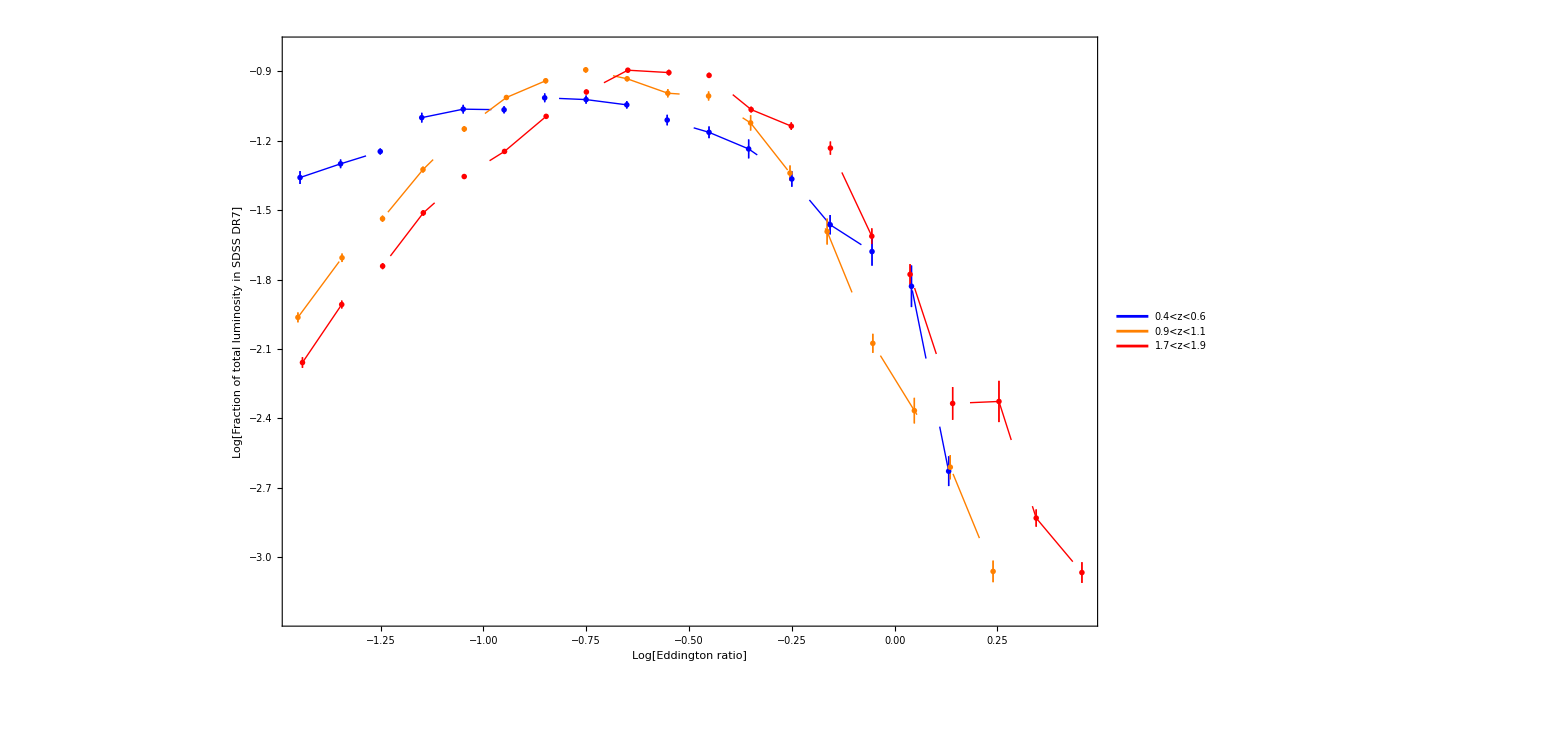

```mathematica
ErrorListPlot[{LumWeightLamdta1,LumWeightLamdta2,LumWeightLamdta3},PlotRange->{-3.25,-0.8},PlotStyle->{{Blue,Thick,Dashing[2]},{Orange,Thick,Dashing[2]},{Red,Thick,Dashing[2]}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},Joined->True,FrameLabel->{"Log[Eddington ratio]","Log[Fraction of total luminosity in SDSS DR7]"},PlotOptions1,PlotMarkers->{{marker1,0.015},{marker2,0.015},{marker3,0.015}}, Epilog->{Inset[Grid[{linea[Blue,{},5,0.1,Style["0.4<z<0.6",FontFamily->Helvetica]],linea[Orange,{},5,0.1,Style["0.9<z<1.1",FontFamily->Helvetica]],linea[Red,{},5,0.1,Style["1.7<z<1.9",FontFamily->Helvetica]]},Spacings->{0,0},Alignment-> Left],{-1.05,-2.9}]},ImageSize->1200]
```

## Taking into account error due to measurment

```mathematica
(*What this functions does: 1. Takes data and models the distribution of objects in a 0.1 dex luminosity bins as a log-normal distribution; estimates mean and sigma of the distribution for each lumnosity bin. 2. fits a linear function (called 'f' in the code) which estimates dependence of sigma as a function of luminosity (this step is optional; one can also work with dirrectly estimated sigmas, but this makes things a bit smoother) 3. Creates random objects given the means estimated in step 1 and with sigmas estimated as σ_new^2=σ_measured^2-convolution_error^2*)
```

```mathematica
f
```

2.63854-0.0483684 x

```mathematica
fDeconvolving[inputdata_,assumederror_]:=Block[{},test=Flatten[DeleteCases[Table[{If[help=Length[Select[inputdata,i<#[[2]]<(i+0.1)&][[All,3]]];help>10,{i+0.05,help,FindDistributionParameters[Select[data05,i<#[[2]]<(i+0.1)&][[All,3]],NormalDistribution[μ,σ]][[All,2]]},##&[]]},{i,45.2,47,0.1}],{}],1];f=Fit[{test[[All,1]],test[[All,3]][[All,2]]}//Transpose,{1,x},x];Flatten[Table[{RandomVariate[UniformDistribution[{test[[i,1]]-0.05,test[[i,1]]+0.05}],test[[i,2]]],RandomVariate[NormalDistribution[test[[i,3,1]],If[ressigma=Sqrt[(f/.x->test[[i,1]])^2-assumederror^2];Re[ressigma]>0.01,ressigma,0.01]],test[[i,2]]]}//Transpose,{i,Length[test]}],1]]
```

```mathematica
data05Recreated=fDeconvolving[data05,0.0];
data05Recreated01=fDeconvolving[data05,0.1];
data05Recreated02=fDeconvolving[data05,0.2];
data05Recreated03=fDeconvolving[data05,0.3];
```

```mathematica
data10Recreated=fDeconvolving[data10,0.0];
data10Recreated01=fDeconvolving[data10,0.1];
data10Recreated02=fDeconvolving[data10,0.2];
data10Recreated03=fDeconvolving[data10,0.3];
```

```mathematica
data18Recreated=fDeconvolving[data18,0.0];
data18Recreated01=fDeconvolving[data18,0.1];
data18Recreated02=fDeconvolving[data18,0.2];
data18Recreated03=fDeconvolving[data18,0.3];
```

#### Plot showing Ed. ratio distributions with convolution effects

```mathematica
datazRec={data05Recreated,data10Recreated,data18Recreated};
datazRec01={data05Recreated01,data10Recreated01,data18Recreated01};
datazRec02={data05Recreated02,data10Recreated02,data18Recreated02};
datazRec03={data05Recreated03,data10Recreated03,data18Recreated03};
```

```mathematica
dataz={data05,data10,data18};
j=1;SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta1=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=2;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta2=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=3;
SplitByEddRatio=Table[Select[{dataz[[j]][[All,2]],dataz[[j]][[All,3]],(dataz[[j]][[All,2]]-38.1-dataz[[j]][[All,3]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta3=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];

dataz=datazRec;
j=1
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta1Rec=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=2
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta2Rec=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=3
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta3Rec=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];

dataz=datazRec01;
j=1
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta1Rec01=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=2
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta2Rec01=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=3
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta3Rec01=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];

dataz=datazRec02;
j=1
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta1Rec02=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=2
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta2Rec02=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=3
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta3Rec02=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];

dataz=datazRec03;
j=1
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta1Rec03=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=2
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta2Rec03=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
j=3
SplitByEddRatio=Table[Select[{dataz[[j]][[All,1]],dataz[[j]][[All,2]],(dataz[[j]][[All,1]]-38.1-dataz[[j]][[All,2]])}//Transpose,(-1.5+i*0.1)<#[[3]]<(-1.4+i*0.1)&],{i,0,20}];
LumWeightLamdta3Rec03=Table[{Mean[SplitByEddRatio[[i]][[All,3]]],Log10[Total[Power[10,SplitByEddRatio[[i]][[All,1]]]]]},{i,20}];
```

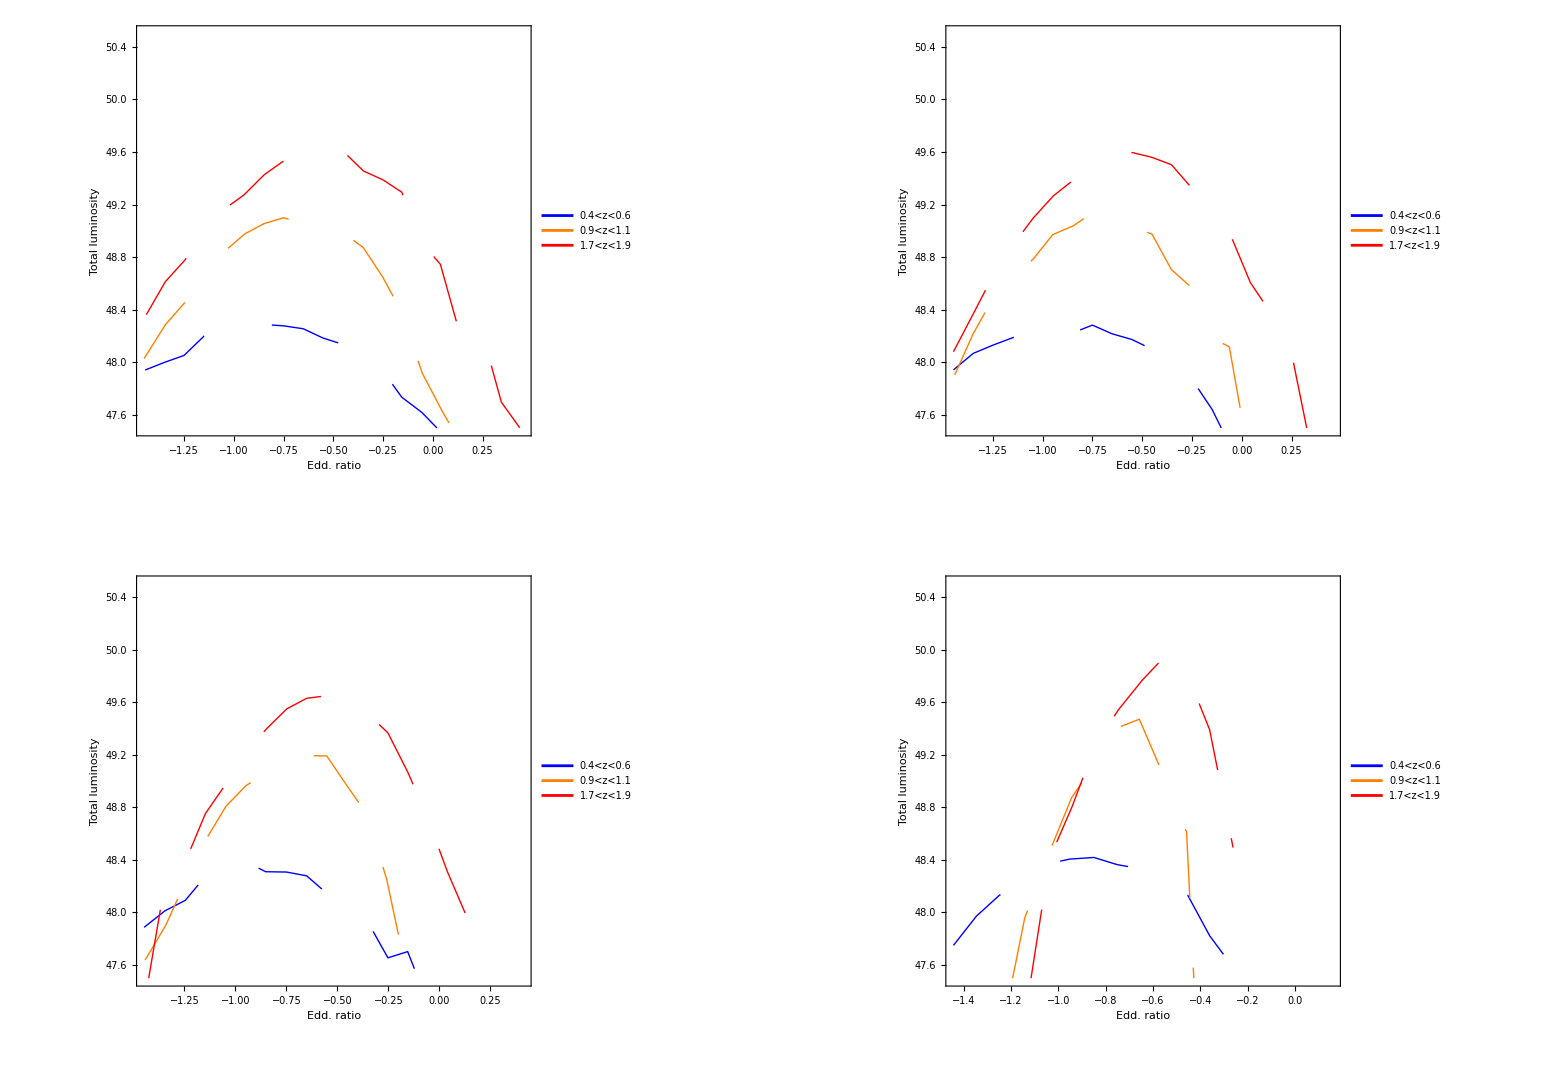

```mathematica
GraphicsGrid[{{ListPlot[{LumWeightLamdta1,LumWeightLamdta2,LumWeightLamdta3},PlotRange->{47.5,50.5},PlotStyle->{{Blue,Thick,Dashing[2]},{Orange,Thick,Dashing[2]},{Red,Thick,Dashing[2]}},Frame->True,Joined->True,FrameLabel->{"Edd. ratio","Total luminosity","Shen+ 2011, no correction"},ImageSize->800,{FrameTicks->{LinTicks,LinTicks,None,None},FrameStyle->Directive[Thickness[Large],Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{20,FontFamily->"Helvetica"}},Epilog->{Inset[Grid[{linea[Blue,{},5,0.1,Style["0.4<z<0.6",FontFamily->Helvetica]],linea[Orange,{},5,0.1,Style["0.9<z<1.1",FontFamily->Helvetica]],linea[Red,{},5,0.1,Style["1.7<z<1.9",FontFamily->Helvetica]]},Spacings->{0,0},Alignment-> Left],{-1.05,50.13}]}],ListPlot[{LumWeightLamdta1Rec01,LumWeightLamdta2Rec01,LumWeightLamdta3Rec01},PlotRange->{47.5,50.5},PlotStyle->{{Blue,Thick,Dashing[2]},{Orange,Thick,Dashing[2]},{Red,Thick,Dashing[2]}},Frame->True,Joined->True,FrameLabel->{"Edd. ratio","Total luminosity","Shen+ 2011, \"correction\" of 0.1 dex"},ImageSize->800,{FrameTicks->{LinTicks,LinTicks,None,None},FrameStyle->Directive[Thickness[Large],Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{20,FontFamily->"Helvetica"}},Epilog->{Inset[Grid[{linea[Blue,{},5,0.1,Style["0.4<z<0.6",FontFamily->Helvetica]],linea[Orange,{},5,0.1,Style["0.9<z<1.1",FontFamily->Helvetica]],linea[Red,{},5,0.1,Style["1.7<z<1.9",FontFamily->Helvetica]]},Spacings->{0,0},Alignment-> Left],{-1.05,50.13}]}]},{ListPlot[{LumWeightLamdta1Rec02,LumWeightLamdta2Rec02,LumWeightLamdta3Rec02},PlotRange->{47.5,50.5},PlotStyle->{{Blue,Thick,Dashing[2]},{Orange,Thick,Dashing[2]},{Red,Thick,Dashing[2]}},Frame->True,Joined->True,FrameLabel->{"Edd. ratio","Total luminosity","Shen+ 2011, \"correction\" of 0.2 dex"},ImageSize->800,{FrameTicks->{LinTicks,LinTicks,None,None},FrameStyle->Directive[Thickness[Large],Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{20,FontFamily->"Helvetica"}},Epilog->{Inset[Grid[{linea[Blue,{},5,0.1,Style["0.4<z<0.6",FontFamily->Helvetica]],linea[Orange,{},5,0.1,Style["0.9<z<1.1",FontFamily->Helvetica]],linea[Red,{},5,0.1,Style["1.7<z<1.9",FontFamily->Helvetica]]},Spacings->{0,0},Alignment-> Left],{-1.05,50.13}]}],ListPlot[{LumWeightLamdta1Rec03,LumWeightLamdta2Rec03,LumWeightLamdta3Rec03},PlotRange->{47.5,50.5},PlotStyle->{{Blue,Thick,Dashing[2]},{Orange,Thick,Dashing[2]},{Red,Thick,Dashing[2]}},Frame->True,Joined->True,FrameLabel->{"Edd. ratio","Total luminosity","Shen+ 2011, \"correction\" of 0.3 dex"},ImageSize->800,{FrameTicks->{LinTicks,LinTicks,None,None},FrameStyle->Directive[Thickness[Large],Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{20,FontFamily->"Helvetica"}},Epilog->{Inset[Grid[{linea[Blue,{},5,0.1,Style["0.4<z<0.6",FontFamily->Helvetica]],linea[Orange,{},5,0.1,Style["0.9<z<1.1",FontFamily->Helvetica]],linea[Red,{},5,0.1,Style["1.7<z<1.9",FontFamily->Helvetica]]},Spacings->{0,0},Alignment-> Left],{-1.05,50.13}]}]}}]
```

#### Plot showing differences of distributions in 2d plane

```mathematica
fDeconvolving[inputdata_,assumederror_]:=Block[{},test=Flatten[DeleteCases[Table[{If[help=Length[Select[inputdata,i<#[[2]]<(i+0.1)&][[All,3]]];help>10,{i+0.05,help,FindDistributionParameters[Select[inputdata,i<#[[2]]<(i+0.1)&][[All,3]],NormalDistribution[μ,σ]][[All,2]]},##&[]]},{i,45.2,47.7,0.1}],{}],1];f=Fit[{test[[All,1]],test[[All,3]][[All,2]]}//Transpose,{1,x},x];Flatten[Table[{RandomVariate[UniformDistribution[{test[[i,1]]-0.05,test[[i,1]]+0.05}],test[[i,2]]],RandomVariate[NormalDistribution[test[[i,3,1]],If[ressigma=Sqrt[(f/.x->test[[i,1]])^2-assumederror^2];Re[ressigma]>0.01,ressigma,0.01]],test[[i,2]]]}//Transpose,{i,Length[test]}],1]]
```

```mathematica
fCon2[dataI_]:=Module[{},dist=SmoothKernelDistribution[dataI];Pdff=PDF[dist,{x,y}];data=ParallelTable[{x,y,Pdff},{x,6,12,0.025},{y,43,48,0.025}];maxV=Max[data[[All,3]]];data2=ParallelTable[{i,sel=Select[Flatten[data,1],#[[3]]>i&];Total[sel[[All,3]]]/1600},{i,0,maxV,maxV/20}];Con=Table[{j,FindRoot[j==Interpolation[data2][x],{x,0.5}][[1,2]]},{j,0.1,0.9,0.1}];
Con[[All,2]]]
```

```mathematica
data18For2DPlot={data18[[All,{3,2}]],fDeconvolving[data18,0.0][[All,{2,1}]],fDeconvolving[data18,0.1][[All,{2,1}]],fDeconvolving[data18,0.2][[All,{2,1}]],fDeconvolving[data18,0.3][[All,{2,1}]]};
```

```mathematica
Cons18For2DPlot={fCon2[data18For2DPlot[[1]]],fCon2[data18For2DPlot[[2]]],fCon2[data18For2DPlot[[3]]],fCon2[data18For2DPlot[[4]]],fCon2[data18For2DPlot[[5]]]};
```

```mathematica
ps=0.004;
PlotOptionsML={PlotStyle->{GrayLevel[.1],PointSize[ps]},Frame->True,FrameStyle->Directive[35,Black,Thick],FrameTicksStyle->Directive[25],PlotRange->{{7,10},{44.5,48}},AspectRatio->1,ImageSize->800};
```

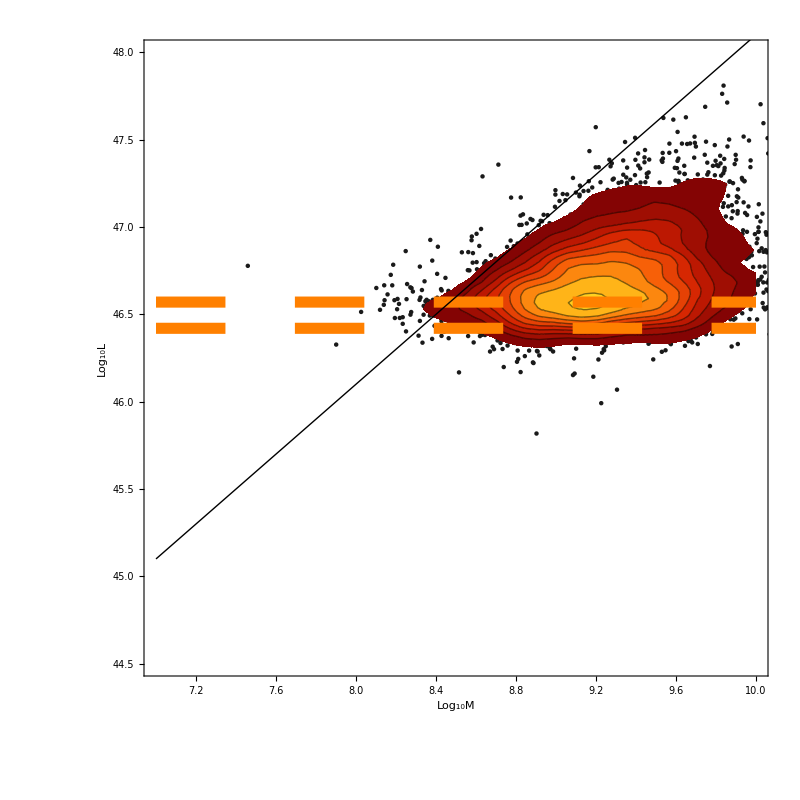

```mathematica
P1=Show[ListPlot[data18For2DPlot[[1]],FrameLabel->{"Log_10M","Log_10L","Data, z=1.7-1.9"},Evaluate[PlotOptionsML]],ContourPlot[Evaluate[PDF[SmoothKernelDistribution[data18For2DPlot[[1]]],{x,y}]],{x,7,10},{y,44.5,48},ColorFunction->"SolarColors",FrameStyle->Directive[Large],ImageSize->500,RegionFunction->Function[{x,y,z},z>Last[Cons18For2DPlot[[1]]]],ColorFunction->"SunsetColors",PlotPoints->10,Contours->Cons18For2DPlot[[1]]],Plot[46.42,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[46.57,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[x+38.1,{x,7,10},PlotStyle->{Black,Thick}]]
```

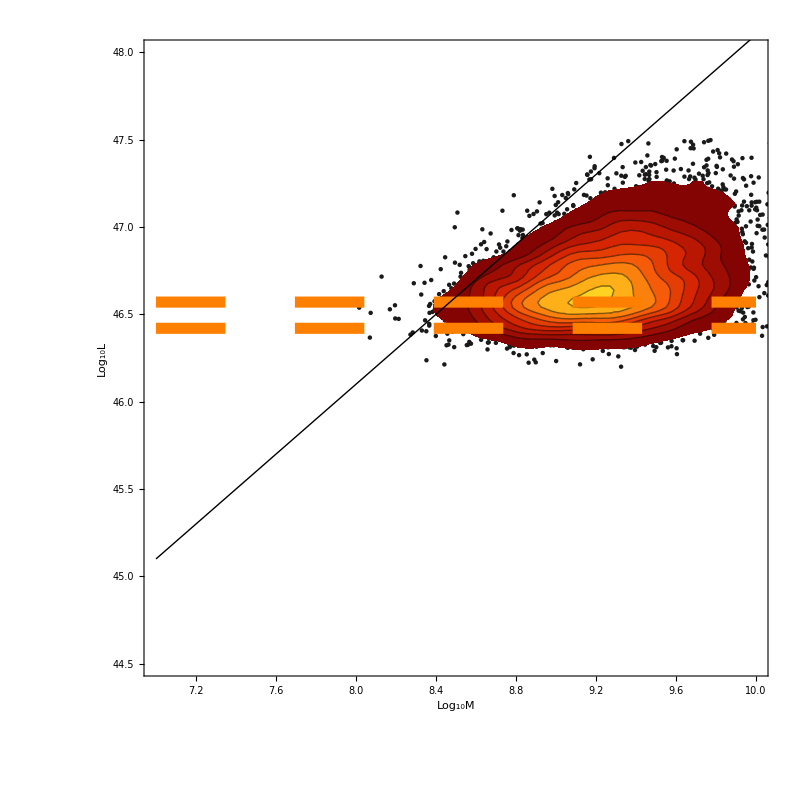

```mathematica
P2=Show[ListPlot[data18For2DPlot[[2]],FrameLabel->{"Log_10M","Log_10L","Model, no convolution, z=1.7-1.9"},Evaluate[PlotOptionsML]],ContourPlot[Evaluate[PDF[SmoothKernelDistribution[data18For2DPlot[[2]]],{x,y}]],{x,7,10},{y,44.5,48},ColorFunction->"SolarColors",FrameStyle->Directive[Large],ImageSize->500,RegionFunction->Function[{x,y,z},z>Last[Cons18For2DPlot[[2]]]],ColorFunction->"SunsetColors",PlotPoints->10,Contours->Cons18For2DPlot[[2]]],Plot[46.42,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[46.57,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[x+38.1,{x,7,10},PlotStyle->{Black,Thick}]]
```

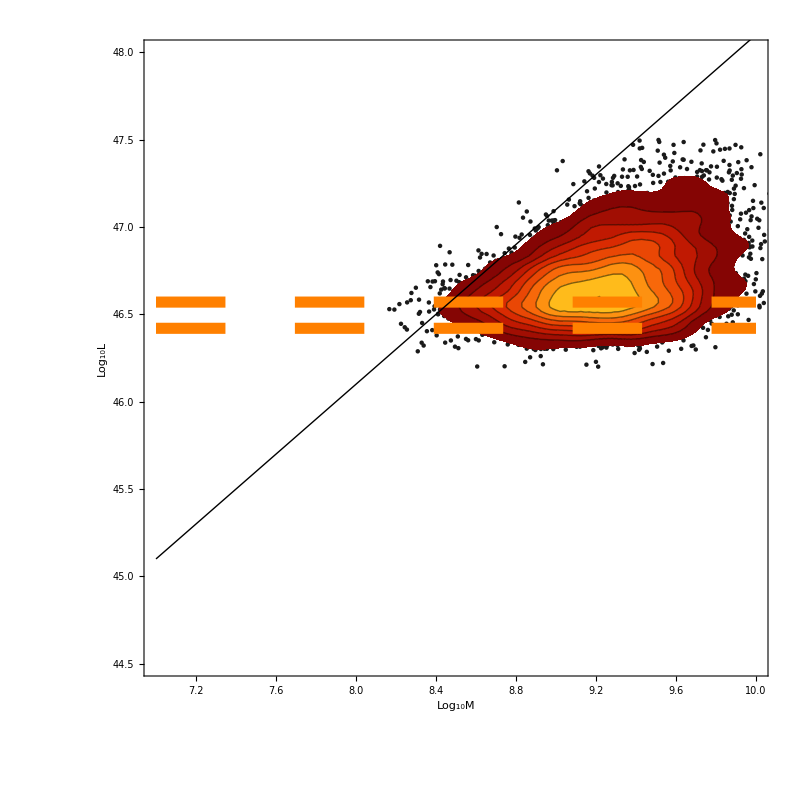

```mathematica
P3=Show[ListPlot[data18For2DPlot[[3]],FrameLabel->{"Log_10M","Log_10L","Before convolution with 0.1 dex, z=1.7-1.9"},Evaluate[PlotOptionsML]],ContourPlot[Evaluate[PDF[SmoothKernelDistribution[data18For2DPlot[[3]]],{x,y}]],{x,7,10},{y,44.5,48},ColorFunction->"SolarColors",FrameStyle->Directive[Large],ImageSize->500,RegionFunction->Function[{x,y,z},z>Last[Cons18For2DPlot[[3]]]],ColorFunction->"SunsetColors",PlotPoints->10,Contours->Cons18For2DPlot[[3]]],Plot[46.42,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[46.57,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[x+38.1,{x,7,10},PlotStyle->{Black,Thick}]]
```

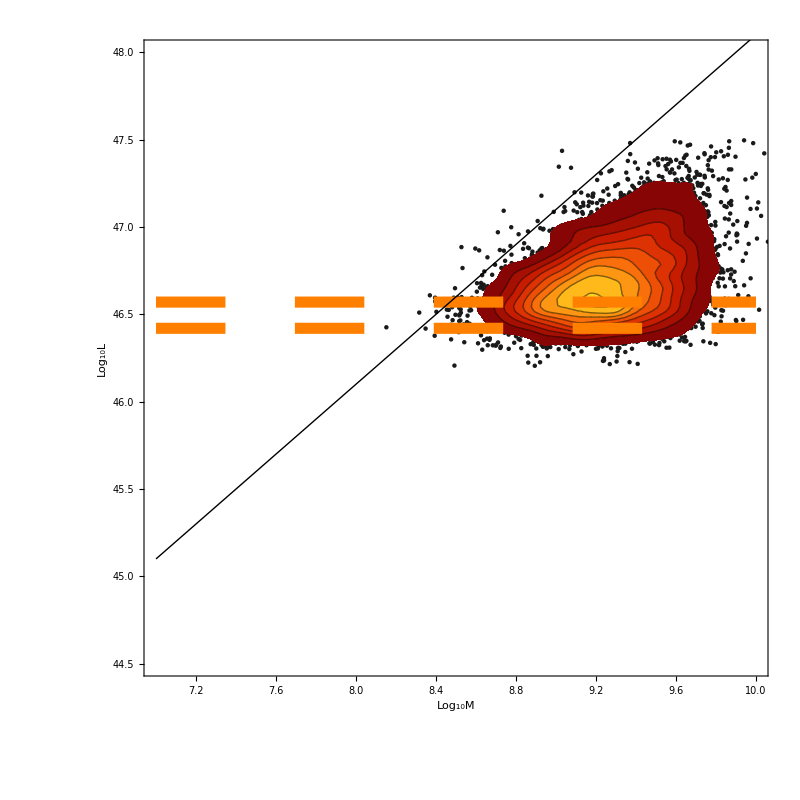

```mathematica
P4=Show[ListPlot[data18For2DPlot[[4]],FrameLabel->{"Log_10M","Log_10L","Before convolution with 0.2 dex, z=1.7-1.9"},Evaluate[PlotOptionsML]],ContourPlot[Evaluate[PDF[SmoothKernelDistribution[data18For2DPlot[[4]]],{x,y}]],{x,7,10},{y,44.5,48},ColorFunction->"SolarColors",FrameStyle->Directive[Large],ImageSize->500,RegionFunction->Function[{x,y,z},z>Last[Cons18For2DPlot[[4]]]],ColorFunction->"SunsetColors",PlotPoints->10,Contours->Cons18For2DPlot[[4]]],Plot[46.42,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[46.57,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[x+38.1,{x,7,10},PlotStyle->{Black,Thick}]]
```

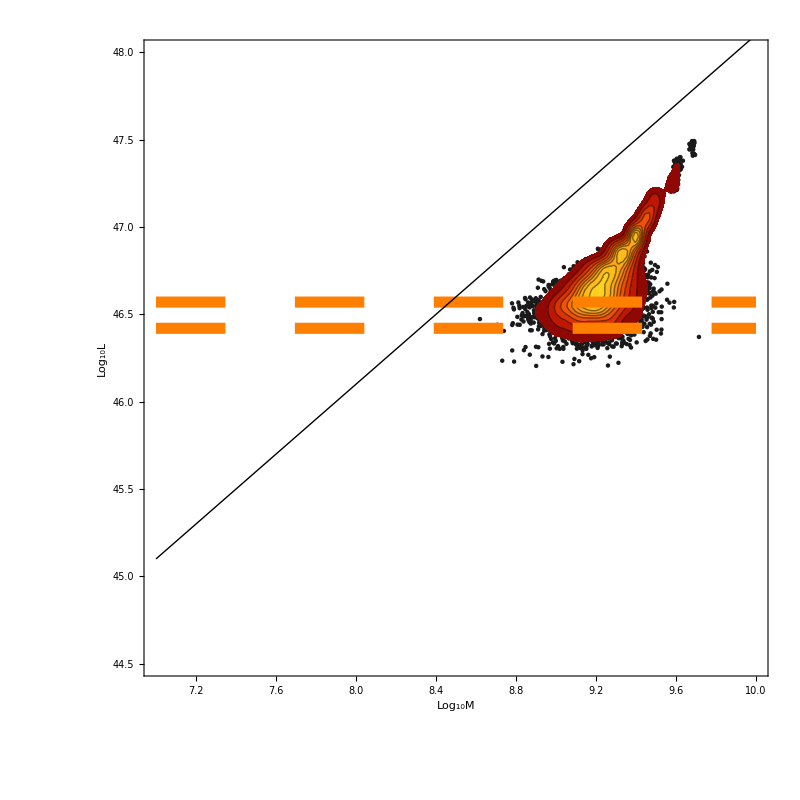

```mathematica
P5=Show[ListPlot[data18For2DPlot[[5]],FrameLabel->{"Log_10M","Log_10L","Before convolution with 0.3 dex, z=1.7-1.9"},Evaluate[PlotOptionsML]],ContourPlot[Evaluate[PDF[SmoothKernelDistribution[data18For2DPlot[[5]]],{x,y}]],{x,7,10},{y,44.5,48},ColorFunction->"SolarColors",FrameStyle->Directive[Large],ImageSize->500,RegionFunction->Function[{x,y,z},z>Last[Cons18For2DPlot[[5]]]],ColorFunction->"SunsetColors",PlotPoints->10,Contours->Cons18For2DPlot[[5]]],Plot[46.42,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[46.57,{x,7,10},PlotStyle->{Orange,Dashing[.2],Thickness[0.01]}],Plot[x+38.1,{x,7,10},PlotStyle->{Black,Thick}]]
```

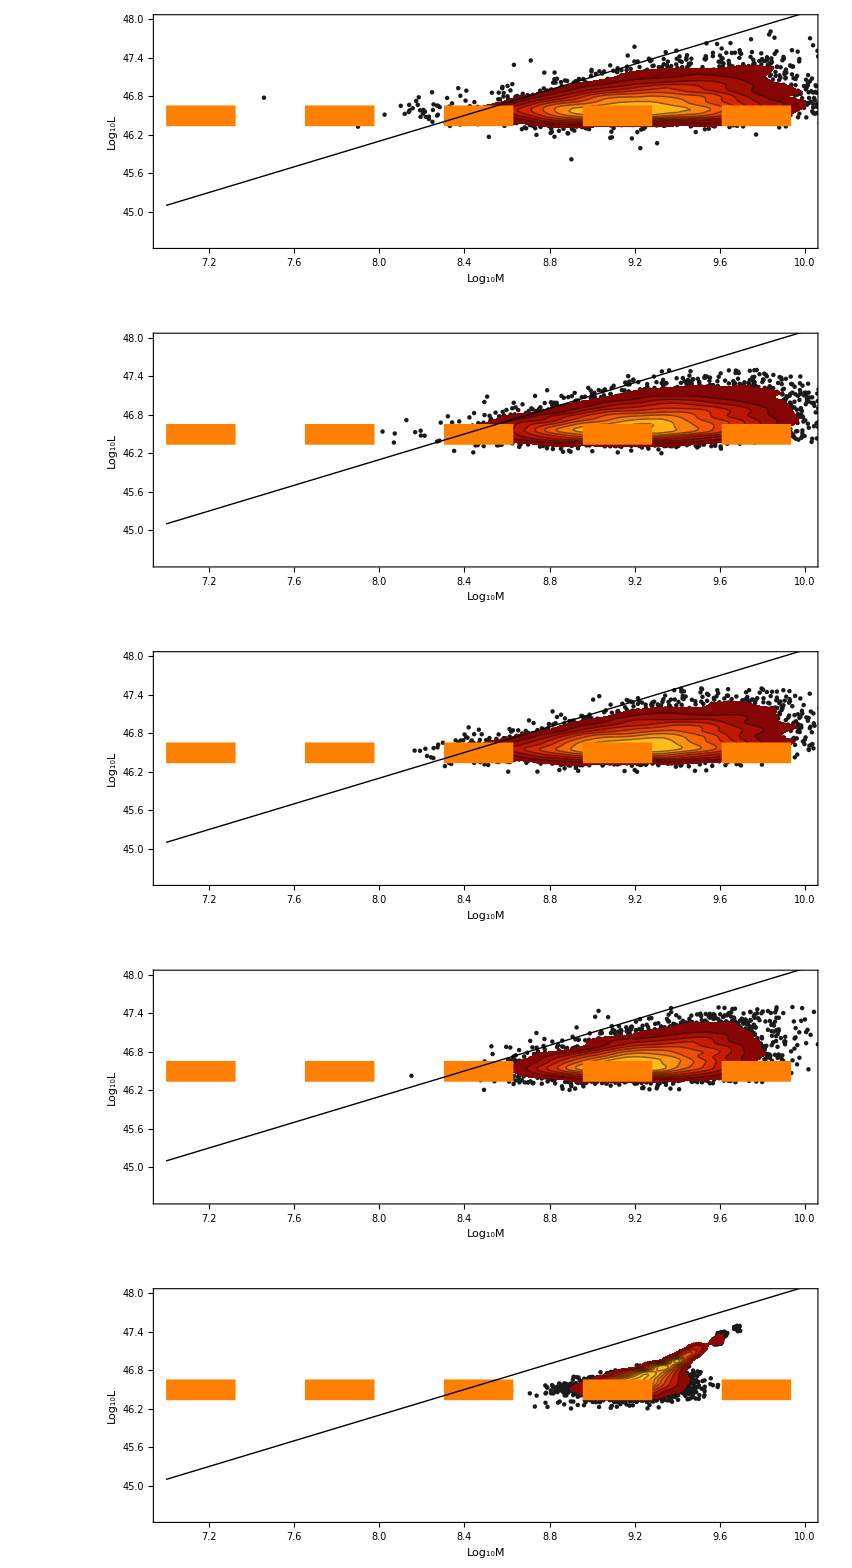

```mathematica
GraphicsColumn[{P1,P2,P3,P4,P5}]
```